```mathematica
"Here we have a return amplitude of the form (NNN)^(-h).  To compute the probablity amplitudes we need the Lanczos coefficients and derivatives of the return amplitude (at a desired point in time).  To compute the derivative I have found it more efficient to compute deriviates of NNN and plug it into an expression for the general derivative of (F(t))^(-h).  There may be ways to do this even faster though"
```

```mathematica
"Here is a test function - analytic results are possible for this so we can compare it with known expressions"
```

```mathematica
varSub = {h->1, c->1/2, ω->1/3};   NNN = Cos[ω t] + I c/ω Sin[ω t];  ReturnAmpt = NNN^(-h)/.varSub;  NNNNum = NNN/.varSub;    Genf =  F[t]^(-h)/.varSub;
```

## Initialization functions

```mathematica
(*For Ising Matrix. Given a binary number occupation rep of spins, it gives the corresponding matrix*)
SpinStateMatrix[OccRep_, Spin_] := Module[{a}, 
a=IdentityMatrix[1];
Do[ If[OccRep[[i]]==0, a = KroneckerProduct[a,IdentityMatrix[Dimensions[Spin]]]];
If[OccRep[[i]]==1, a = KroneckerProduct[a, Spin]];
,{i, 1, Length[OccRep]}];
a]
```

```mathematica
(*For Ising Matrix. Given Length, Interaction Spins, Number of Interaction Spins (k-local), And the Spins for 2 magnetic fields, it Generates the Matrix representation.*)
IsingSum[L_,IntSpin_,IntSpinNo_,BSpin1_,BSpin2_]:=Module[{IntPerms, IntPieces, IntPart, B1Part, B2Part, SingleSpinPerms, B1Pieces, B2Pieces},
IntPerms = Table[Join[ConstantArray[0,i-1],ConstantArray[1,IntSpinNo],ConstantArray[0,L-(i-1)-IntSpinNo]],{i,1,L-IntSpinNo+1}];
SingleSpinPerms=Table[Join[ConstantArray[0,i-1],ConstantArray[1,1],ConstantArray[0,L-(i-1)-1]],{i,1,L}];
If[IntSpin == 0, IntPart = IntSpin, IntPart =IntSpin,
IntPieces = Table[SpinStateMatrix[IntPerms[[i]], IntSpin],{i, 1, Length[IntPerms]}];
IntPart = Total[IntPieces]];
If[BSpin1 == 0, B1Part=BSpin1,B1Part=BSpin1,
B1Pieces=Table[SpinStateMatrix[SingleSpinPerms[[i]],BSpin1],{i,1,Length[SingleSpinPerms]}];
B1Part = Total[B1Pieces]];
If[BSpin2 == 0, B2Part = BSpin2,B2Part=BSpin2,
B2Pieces =Table[SpinStateMatrix[SingleSpinPerms[[j]],BSpin2],{j,1,Length[SingleSpinPerms]}];
B2Part = Total[B2Pieces]];
IntPart+B1Part+B2Part]
```

## Choose H and State

```mathematica
p1 =PauliMatrix[1];p2=PauliMatrix[2];p3=PauliMatrix[3];Id = IdentityMatrix[2];
```

```mathematica
H = IsingSum[4,p3,2,p1,0];
```

```mathematica
U[t_] := MatrixExp[-I*t*H];
```

```mathematica
Op = IsingSum[4,0,0,p3,0];
```

```mathematica
State = Table[Op[[1]][[i]],{i,1,Length[Op]}];
```

## Calculate the Return Amplitude

```mathematica
NNNexpr = N[FullSimplify[ConjugateTranspose[State].MatrixExp[-I*t*H].State],50]
```

1.3333333333333333333333333333333333333333333333333 (0.14200734925348727882830497942442595870869367424493 2.7182818284590452353602874713526624977572470937^((0.-0.30540728933227860459313349292274081599849729126372 ⅈ) t)+0.094372860952649518964620883772320965419140508682186 2.7182818284590452353602874713526624977572470937^((0.+0.30540728933227860459313349292274081599849729126372 ⅈ) t)+2.7182818284590452353602874713526624977572470937^((0.+1. ⅈ) t)+0.36610868398461772806417020124825304679550265541797 2.7182818284590452353602874713526624977572470937^((0.-1.6945927106677213954068665070772591840015027087363 ⅈ) t)+2.7636197897938632022070741368032530758721658170729 2.7182818284590452353602874713526624977572470937^((0.-2.0641777724759121408095706022216666957433298283216 ⅈ) t)+0.094372860952649518964620883772320965419140508682186 2.7182818284590452353602874713526624977572470937^((0.+2.0641777724759121408095706022216666957433298283216 ⅈ) t)+0.066446816951594790224421043361728448084304466612575 2.7182818284590452353602874713526624977572470937^((0.+2.7587704831436335362164371092989258797448325370579 ⅈ) t)+4.5674444990637874817114087553900185051201928779695 2.7182818284590452353602874713526624977572470937^((0.-4.0641777724759121408095706022216666957433298283216 ⅈ) t)+2.7636197897938632022070741368032530758721658170729 2.7182818284590452353602874713526624977572470937^((0.-4.7587704831436335362164371092989258797448325370579 ⅈ) t)+0.14200734925348727882830497942442595870869367424493 2.7182818284590452353602874713526624977572470937^((0.+4.7587704831436335362164371092989258797448325370579 ⅈ) t))

```mathematica
NNNexpr = FullSimplify[ConjugateTranspose[State].MatrixExp[I*t*H].State]
```

1/3 ⅇ^(-ⅈ t) (4+ⅇ^(t Root-1.06 ⅈRoot[64+96 #1^2+36 #1^4+#1^6&,1]0.) Root0.377Root[-64+288 #1-324 #1^2+27 #1^3&,1]0.37749144381059807+ⅇ^(t Root1.31 ⅈRoot[64+96 #1^2+36 #1^4+#1^6&,6]0.) Root0.568Root[-64+288 #1-324 #1^2+27 #1^3&,2]0.5680293970139492+ⅇ^(t Root5.76 ⅈRoot[64+96 #1^2+36 #1^4+#1^6&,4]0.) Root11.1Root[-64+288 #1-324 #1^2+27 #1^3&,3]11.054479159175452-48 ⅇ^(ⅈ t Root5.06Root[24-6 #1^2+#1^3&,3]5.0641777724759125) Root-0.381Root[1+216 #1+6480 #1^2+15552 #1^3&,1]-0.3806203749219823-48 ⅇ^(ⅈ t Root2.69Root[24-6 #1^2+#1^3&,2]2.694592710667721) Root-0.0305Root[1+216 #1+6480 #1^2+15552 #1^3&,2]-0.030509056998718143-48 ⅇ^(ⅈ t Root-1.76Root[24-6 #1^2+#1^3&,1]-1.7587704831436335) Root-5.54 × 10^-3Root[1+216 #1+6480 #1^2+15552 #1^3&,3]-0.005537234745966233+48 ⅇ^(ⅈ t Root0.695Root[8-12 #1+#1^3&,2]0.6945927106677214) Root7.86 × 10^-3Root[-1+216 #1-11664 #1^2+46656 #1^3&,1]0.00786440507938746+48 ⅇ^(ⅈ t Root-3.76Root[8-12 #1+#1^3&,1]-3.7587704831436337) Root0.0118Root[-1+216 #1-11664 #1^2+46656 #1^3&,2]0.01183394577112394+48 ⅇ^(ⅈ t Root3.06Root[8-12 #1+#1^3&,3]3.064177772475912) Root0.230Root[-1+216 #1-11664 #1^2+46656 #1^3&,3]0.2303016491494886)

```mathematica
Clear[NNN]
```

```mathematica
NNN[t_]:= N[FullSimplify[ConjugateTranspose[State].U[t].State],50]
```

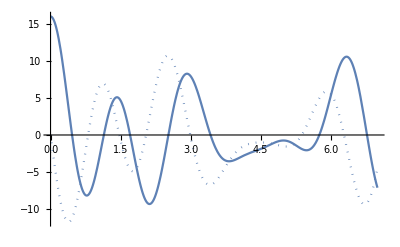

```mathematica
ReImPlot[NNN[t],{t,0,7}]
```

```mathematica
ReturnAmpt = NNN;  NNNNum = NNN;    Genf =  F[t];
```

```mathematica
Series[NNN[t],{t,0,3}]
```

16.-(0.+48. ⅈ) t-(104.+0. ⅈ) t^2+(0.+136. ⅈ) t^3+O[t]^4

```mathematica
SeriesCoefficient[ReturnAmpt[t],{t,0,3}]
```

0.+136. ⅈ

## Lanczos Coeffs via Moments Method

```mathematica
"To compute the Lanczos coefficients we need a package called Combinatrica which contains the function "
```

```mathematica
Needs["Combinatorica`"]
```

```mathematica
"nnn denotes the number of derivatives we will be taking - the number of Lanczos coefficients one generates is nnn/2.  This loop here computes the Lanczos coefficients via the moments method"
```

```mathematica
Clear[ϕn, NNND, NNNDTab, ϕt, PPlot, NNNn];
```

```mathematica
nnn = 13; 
NNNn[t_] := Simplify[Series[ReturnAmpt[t], {t, 0, nnn} ]]
```

```mathematica
μTab = Table[Factorial[j]SeriesCoefficient[ NNNn[t], j], {j, 0, nnn}];
```

```mathematica
MijR = Simplify[   Sum[Table[KroneckerDelta[i+j+1-mm]*μTab[[mm]], {i, 0, (nnn)/2}, {j, 0, (nnn)/2}], {mm, 1, Length[μTab]}]   ]; bProd = Table[Det[MijR[[1;;k, 1;;k]]      ]/Det[MijR[[1;;(k-1), 1;;(k-1)]]      ], {k, 2, nnn/2+1}];   bTab = Table[If[j==1, Sqrt[- bProd[[j]]   ],  Sqrt[- bProd[[j]]/bProd[[j-1]]    ]   ], {j, 1, Length[bProd]}];    aTab =Table[Simplify[-I(    Simplify[   Cofactor[MijR[[1;;k, 1;;k]], {k-1,k}]/Det[MijR[[1;;k-1, 1;;k-1]]]   ] -    If[k > 2, Simplify[   Cofactor[MijR[[1;;k-1, 1;;k-1]], {k-2,k-1}]/Det[MijR[[1;;k-2, 1;;k-2]]]   ]  , 0])   ]  , {k, 2, Length[bTab]}   ];
```

```mathematica
aTab
```

{3.+0. ⅈ,0.+0. ⅈ,-0.857142857142857142857142857142857142857142857143,-0.53869047619047619047619047619047619047619047619,2.20553208425177565515552289982855743325985794759}

```mathematica
aTab=Re[aTab]
```

{3,0.,-0.857143,-0.53869,2.20553,-0.935853,-0.223874,-0.519827,0.0218167}

```mathematica
bTab
```

{2.,2.64575,2.79942,2.03347,2.21273,1.05864,1.13677,1.5512,0.508354}

## Lanczos Coeffs via Lanczos algorithm

```mathematica
LanczosState[H_, ψ0_, nmax_, tol_] :=
Module[{ψ,ϕ,A,a,b,ANorm, nBreak},
nBreak=nmax;
ψ[1] =ψ0/Sqrt[ConjugateTranspose[ψ0].ψ0];
ϕ[1]= ψ[1];
b[1]=0;
a[1]=0;
Do[ϕ[i+1]=N[  Normal[H].ψ[i]]; A[i+1]=ϕ[i+1]-Sum[(Conjugate[ψ[j]].ϕ[i+1])*ψ[j],{j,1,i}];
ANorm=Sqrt[Conjugate[A[i+1]].A[i+1]] ;
Print[i," and ",ANorm];
If[ANorm< tol,Print["Cut-off reached at ",i];nBreak=i;Break[]];
ψ[i+1]=Chop[A[i+1]/ANorm ];
b[i+1]=Normal[Conjugate[ψ[i+1]].H.ψ[i]];
a[i+1]=Normal[Conjugate[ψ[i]].H.ψ[i]];
,{i,1,nmax}];
{Table[a[i],{i,1,nBreak}],Table[b[i],{i,1,nBreak}]}
(*HKryl = Table[Normal[Conjugate[ψ[i]].H.ψ[j]],{i,1,nBreak},{j,1,nBreak}]*)]
```

```mathematica
LanczosAlgOut = LanczosState[H,State,14,0.001]
```

1 and 2.

2 and 2.64575

3 and 2.79942

4 and 2.03347

5 and 2.21273

6 and 1.05864

7 and 1.13677

8 and 1.5512

9 and 0.508354

10 and 4.93997×10^-15

Cut-off reached at 10

{{0,3,0.,-0.857143,-0.53869,2.20553,-0.935853,-0.223874,-0.519827,0.0218167},{0,2.,2.64575,2.79942,2.03347,2.21273,1.05864,1.13677,1.5512,0.508354}}

```mathematica
aTab = LanczosAlgOut[[1]]
aTab=Delete[aTab,1]
```

{0,3,0.,-0.857143,-0.53869,2.20553,-0.935853,-0.223874,-0.519827,0.0218167}

{3,0.,-0.857143,-0.53869,2.20553,-0.935853,-0.223874,-0.519827,0.0218167}

```mathematica
bTab = LanczosAlgOut[[2]]
bTab=Delete[bTab,1]
```

{0,2.,2.64575,2.79942,2.03347,2.21273,1.05864,1.13677,1.5512,0.508354}

{2.,2.64575,2.79942,2.03347,2.21273,1.05864,1.13677,1.5512,0.508354}

## Complexity

```mathematica
"Here we compute the derivatives at a set of desired points in time.  ϕPts is the number of probabiliyt amplitudes wanted - this should be less than the number of Lanczos coefficients"
```

```mathematica
tMax = 10;   tPts = 50;  ϕPts = 8;   tVals = N[Table[tMax*(i)/(tPts), {i, 1, tPts}], 50];
```

```mathematica
"Here the derivatives are computed at the time-points.  "
```

```mathematica
NNND[0] = NNNexpr;
```

```mathematica
Do[NNND[j+1] =  D[NNND[j][t], t]    , {j, 0, ϕPts-1}  ];
```

```mathematica
NNNDTab = Table[NNND[j]/.t->tVals, {j, 0, ϕPts-1}];
```

```mathematica
FtoNSwap = Table[D[F[t], {t,k}] -> NNNDTab[[k+1]], {k, 0, ϕPts-1}];
```

```mathematica
ϕt = Table[D[ Genf  , {t, k}], {k, 0, ϕPts-1}]/.FtoNSwap;
```

```mathematica
"Here we compute the coefficeints cc and use these along with the derivatives to compute the probabilty amplitudes"
```

```mathematica
Clear[cc];   cc[0,0]=1; cc[0,-1] = 0;    ccPrec=20;
```

```mathematica
Do[  cc[m,n+1]  = N[(If[m≥ 1, I*cc[m-1,n], 0] - If[m≤ n, aTab[[n+1]]*cc[m,n], 0]  - If[m≤n-1 && n>0, bTab[[n]]*cc[m,n-1] , 0 ])/bTab[[n+1]], ccPrec]  , {n, 0, ϕPts}, {m, 0, n+1}   ];
```

```mathematica
PTab = Table[  Sum[ N[N[cc[m,kk], 200]*ϕt[[m+1]], 200], {m, 0, kk}] , {kk, 0, ϕPts-1}];
```

```mathematica
MatrixForm[PTab[[2]]];
```

```mathematica
"The probablity amplitudes can now be combined to compute the total probability"
```

```mathematica
PTab[[2,2]]
```

```mathematica
Abs[PTab[[2,2]]^2]
```

```mathematica
PPlotfirst3= Table[{tVals[[j]],Sum[  Abs[PTab[[k, j]]^2 ] , {k, 1, 3} ] }, {j, 1, Length[tVals]}];
```

```mathematica
ListPlot[PPlotfirst3]
```

-Graphics-

```mathematica
"Here is the sum of all the probabilities we have computed"
```

```mathematica
PPlot= Table[N[{tVals[[j]],Sum[  Abs[PTab[[k, j]]^2 ] , {k, 1, ϕPts} ] },10], {j, 1, Length[tVals]}];
```

$Aborted

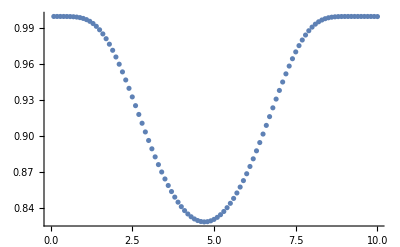

```mathematica
ListPlot[PPlot]
```